```mathematica
Import["/home/zhen/Downloads/03177.dat"]
```

{{125.1,0.3033},{126,0.030036},{128,0.0095468},{130,0.0055619},{135,0.0026081},{140,0.0016339},{145,0.0011235},{150,0.00084879},{160,0.00055631},{170,0.0003944},{180,0.0002974},{190,0.00023744},{200,0.00019557},{210,0.00016513},{220,0.00014017},{230,0.0001235},{240,0.00011083},{250,0.00009756},{260,0.000090235},{270,0.000087629},{280,0.000072817},{290,0.000066224},{300,0.00006094},{310,0.000066504},{320,0.000056465},{330,0.000049424},{340,0.000046204},{350,0.000042746},{360,0.000040275},{370,0.000042532},{380,0.000036466},{390,0.000033955},{400,0.000032027}}

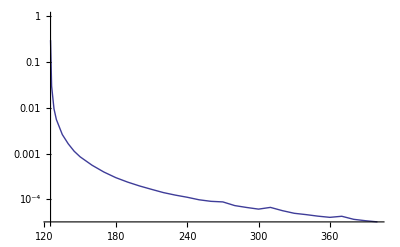

```mathematica
ListLogPlot[%2,Joined->True]
```

```mathematica
data1={{140+5,6 0.03909/17.7^2},{160+5,6 0.02426/17.7^2},{180+5,6 0.01635/17.7^2},{200+5,6 0.01184/17.7^2}}
```

{{145,0.000748635},{165,0.000464617},{185,0.000313128},{205,0.000226755}}

```mathematica
data2={{120+5,6 3184/17.7^2},{120.5+5,6 3.549/17.7^2},{121+5,6 2.025/17.7^2},{122+5,6 1.164/17.7^2},{124+5,6 0.6188/17.7^2},{126+5,6 0.4211/17.7^2},{128+5,6 0.3175/17.7^2},{130+5,6 0.2564/17.7^2},{140+5,6 0.1178/17.7^2},{160+5,6 0.05068/17.7^2},{180+5,6 0.03029/17.7^2},{200+5,6 0.02094/17.7^2},{300+5,6 0.007323/17.7^2},{395+5,6 0.004149/17.7^2}}
```

{{125,60.9786},{125.5,0.067969},{126,0.038782},{127,0.0222924},{129,0.011851},{131,0.00806473},{133,0.00608063},{135,0.00491047},{145,0.00225606},{165,0.000970602},{185,0.000580102},{205,0.000401034},{305,0.000140247},{400,0.0000794599}}

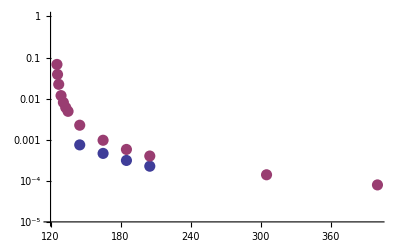

```mathematica
ListLogPlot[{data1,data2},PlotRange->{{120,400},{10^-5,1}},PlotStyle->PointSize[0.02]]
```

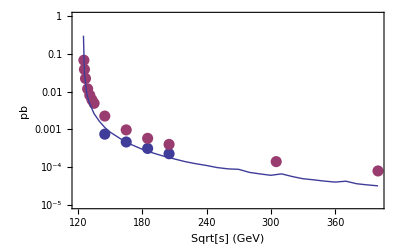

```mathematica
Show[%44,%15,Frame->True,FrameLabel->{"Sqrt[s] (GeV)","pb"}]
```